# Test for VScaling

## Start

```mathematica
(* Add to path packages *)
packageDirectory=FileNameJoin[{NotebookDirectory[],"1DPackage","*"}];
$Path=Join[$Path,FileNames[packageDirectory]];
```

```mathematica
<<"ReadSintel`"
<<"pyramid1d`"

methods={"","OverConstrained","SemiConstrained","Constrained","ConstrainedInitialSign","ConstrainedNewMethod"};
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
```

```mathematica
(* Declare path for SINTEL Data depending on user*)
baseSINTEL=Switch[$UserName,
"fieri","D:\\MastersMathematica\\Data\\Sintel",
"roys","/home/roys/datasets/SINTEL-stereo"
];
```

## Data

```mathematica
(* downscaling *)
r=2;
{ia,ib,id,io}=read[baseSINTEL,"bamboo_1","0001",r,"clean"];

(* {1,44},{1,102} arbitrary size to make the method faster *)
nx=170/r;
ny=300/r;
{ia,ib,id,io}=ImageTake[#,{ny,ny+44},{nx,nx+102}]&/@{ia,ib,id,io}
ImageDimensions[#]&/@{ia,ib,id,io}

max=MinMax[Flatten[ImageData[id]]][[2]];
Print["max dv=", max]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{{103,45},{103,45},{103,45},{103,45}}

max dv=12.5952

## Test

#### Little Functions

```mathematica
pyrfi[ia_,ib_,row_,lvlmax_]:=Block[{pyrfia,pyrfib},
pyrfia=pyrFuncGen[ImageData[ia][[row]], lvlmax];
pyrfib=pyrFuncGen[ImageData[ib][[row]],lvlmax];

Flatten[{pyrfia,pyrfib},{{2},{1},{3}}]
]
```

```mathematica
row=20;
lvlmin=1;
lvlmax=5;

pyrfiab=pyrfi[ia,ib,row,lvlmax];
```

#### Little Test: New method

```mathematica
row=37;

lvlmin=2;
lvlmax=4;
e=0.05;

pyrfiab=pyrfi[ia,ib,row,lvlmax-1];

(* Check solution *)
ic=(*move[ia,-dv]*)ib;
```

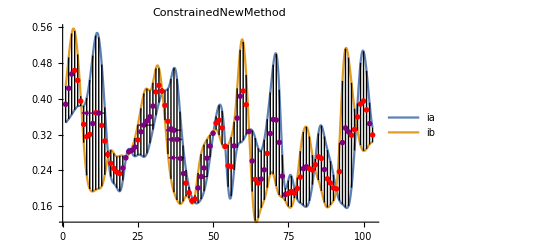

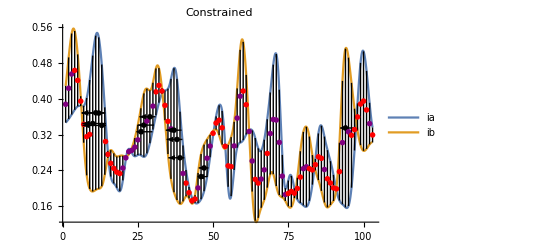

```mathematica
rangex=Range[1,103];

mode="ConstrainedNewMethod";
seeAllLine[rangex,pyrfiab[[lvlmin;;lvlmax]],e*2^(-lvlmin+1),mode]
mode="ConstrainedNewMethod";
seeAllLine[rangex,pyrfiab[[lvlmin;;lvlmax]],e*2^(-lvlmin+1),"Constrained"]
```

#### Little Test: Initial Value Convergence

```mathematica
p=25;
solution=ImageData[id][[row,p]];
```

$Aborted

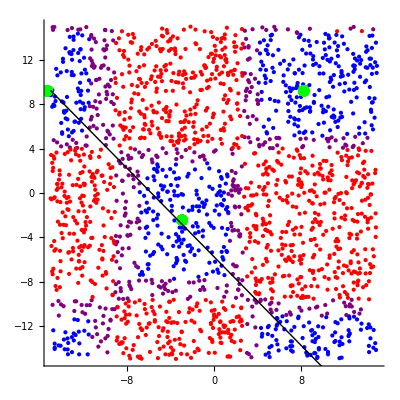

```mathematica
lvlmin=4;
lvlmax=4;
mode="ConstrainedNewMethod";
pixelInitialValueGraphics[10,2000,p,{-15,15},-solution,pyrfiab[[lvlmin;;lvlmax]],e*2^(-lvlmin+1),mode]

lvlmin=4;
lvlmax=4;
mode="Constrained";
pixelInitialValueGraphics[10,2000,p,{-15,15},-solution,pyrfiab[[lvlmin;;lvlmax]],e*2^(-lvlmin+1),mode]
```

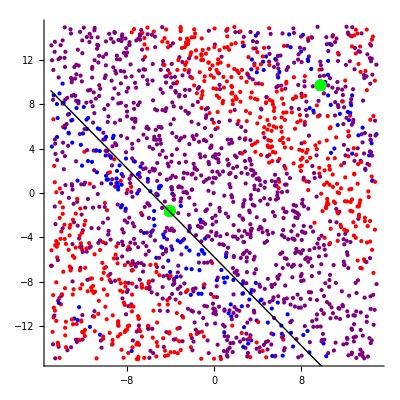

```mathematica
lvlmin=3;
lvlmax=3;
mode="ConstrainedNewMethod";
pixelInitialValueGraphics[10,2000,p,{-15,15},-solution,pyrfiab[[lvlmin;;lvlmax]],e*2^(-lvlmin+1),mode]
```